# HW 5

#### Shahaf Zohar - 205978000 Roey Salah-206115438‏

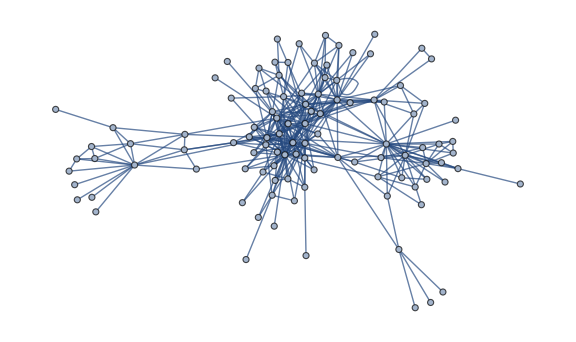

```mathematica
SetDirectory[NotebookDirectory[]];
file = Rest[Import["stormofswords.csv"]];
tribes = Import["tribes.csv"];
nodes =Flatten[tribes[[All,1]]];
edges =#[[1]]<->#[[2]]&/@ file [[All,{1,2}]];
GWight =Graph[nodes,edges,EdgeWeight->file[[All,3]]];
T =Graph[nodes,edges]
```

PercolationCentrality is a graph centrality measure that quantifies the vulnerability of a network to targeted attacks . Specifically, it measures how much the removal of nodes from a graph affects the connectivity of the remaining nodes . The idea behind percolation centrality is to simulate the process of randomly removing nodes from a graph and measuring the size of the largest connected component in the remaining graph at each step . The nodes that, when removed, cause the largest drops in the size of the largest connected component are considered the most important nodes in terms of percolation centrality .

Centrality measures for "Network of Thrones"

# With weight

### Degree centrality

```mathematica
degreeCentralityW=Transpose[{Part[VertexList[GWight],Ordering[DegreeCentrality[GWight],7,Greater]],Part[DegreeCentrality[GWight],Ordering[DegreeCentrality[GWight],7,Greater]]}];
PieChart3D[degreeCentralityW[[All,2]],ChartLabels->degreeCentralityW[[All,1]],ChartStyle->"Pastel",PlotTheme->"Business",ImageSize->Medium]
```

-Graphics3D-

### Betweenness Centrality

```mathematica
betweennessCentralityW=Transpose[{Part[VertexList[GWight],Ordering[BetweennessCentrality[GWight],7,Greater]],Part[BetweennessCentrality[GWight],Ordering[BetweennessCentrality[GWight],7,Greater]]}];

PieChart3D[betweennessCentralityW[[All,2]],ChartLabels->degreeCentralityW[[All,1]],ChartStyle->"Pastel",PlotTheme->"Business",ImageSize->Medium]
```

-Graphics3D-

### Closeness Centrality

```mathematica
closenessCentralityW=Transpose[{Part[VertexList[GWight],Ordering[ClosenessCentrality[GWight],7,Greater]],Part[ClosenessCentrality[GWight],Ordering[ClosenessCentrality[GWight],7,Greater]]}];

PieChart3D[closenessCentralityW[[All,2]],ChartLabels->degreeCentralityW[[All,1]],ChartStyle->"Pastel",PlotTheme->"Business",ImageSize->Medium]
```

-Graphics3D-

### Page Rank Centrality

```mathematica
pageCentralityW=
Transpose[{Part[VertexList[GWight],Ordering[PageRankCentrality[GWight],7,Greater]],Part[PageRankCentrality[GWight],Ordering[PageRankCentrality[GWight],7,Greater]]}];

PieChart3D[pageCentralityW[[All,2]],ChartLabels->degreeCentralityW[[All,1]],ChartStyle->"Pastel",PlotTheme->"Business",ImageSize->Medium]
```

-Graphics3D-

### Eigen Vector Centrality

```mathematica
eigenvectorCentralityW=Transpose[{Part[VertexList[GWight],Ordering[EigenvectorCentrality[GWight],7,Greater]],Part[EigenvectorCentrality[GWight],Ordering[EigenvectorCentrality[GWight],7,Greater]]}];

PieChart3D[eigenvectorCentralityW[[All,2]],ChartLabels->degreeCentralityW[[All,1]],ChartStyle->"Pastel",PlotTheme->"Business",ImageSize->Medium]
```

-Graphics3D-

# Without weight

We calculated Centrality for a graph without weights, for each vertex

```mathematica
(*Compute degree centrality*)
degreeCentrality=VertexDegree[T]/(VertexCount[T]-1);
(*Compute betweenness centrality*)
betweennessCentrality=BetweennessCentrality[T];
(*Compute eigenvector centrality*)
eigenvectorCentrality = EigenvectorCentrality[T];
(*Compute closeness centrality*)
closenessCentrality = ClosenessCentrality[T];
(*Compute Page Rank centrality*)
pagerankCentrality = PageRankCentrality[T];
```

```mathematica
(*Print the results*)
Print["Degree centrality: ",degreeCentrality];
Print["================================================================="];
Print["Betweenness centrality: ",betweennessCentrality];
Print["================================================================="];
Print["Closeness centrality: ",closenessCentrality];
Print["================================================================="];
Print["Eigenvector centrality: ",eigenvectorCentrality];
Print["================================================================="];
Print["page Rank centrality: ",pagerankCentrality];
Print["================================================================="];
```

Degree centrality: {1/106,5/106,2/53,3/106,1/106,1/53,19/106,3/53,3/53,2/53,3/53,1/53,7/53,7/106,2/53,5/53,9/53,10/53,1/53,5/106,1/106,2/53,7/53,3/106,5/106,1/106,2/53,6/53,3/106,4/53,5/106,1/53,2/53,2/53,6/53,2/53,2/53,3/106,1/106,3/53,2/53,12/53,3/53,1/53,9/53,2/53,13/53,1/53,3/53,1/106,3/53,1/106,1/106,9/106,5/106,1/53,5/53,3/106,6/53,7/106,3/106,5/106,2/53,7/106,1/53,2/53,1/53,7/106,1/53,1/106,7/106,5/106,2/53,5/106,1/106,1/106,1/106,2/53,4/53,3/53,1/53,3/53,25/106,9/53,3/106,2/53,2/53,1/106,15/106,13/106,13/53,5/106,1/106,7/53,1/53,2/53,5/106,5/106,18/53,11/53,2/53,7/106,3/106,4/53,1/106,1/106,2/53}

=================================================================

Betweenness centrality: {0.,25.7243,0.,0.,0.,0.,443.014,3.49547,223.235,105.,3.38976,0.,350.687,8.55674,0.583333,26.3065,272.161,148.844,0.,105.,0.,0.333333,874.837,0.,312.,0.,0.333333,107.635,0.,35.1554,16.6775,0.,0.,0.,32.7217,0.333333,12.2081,1.35026,0.,0.,1.,556.185,131.104,0.,141.541,2.2619,1279.75,3.20799,12.9658,0.,106.959,0.,0.,21.0399,3.67319,0.,84.6723,0.,40.4907,6.10677,0.,11.0869,47.9072,1.44137,0.,3.47032,0.,108.963,0.,0.,6.40094,4.65178,0.,1.46667,0.,0.,0.,0.,23.5284,40.695,0.,4.24405,706.557,1165.6,0.,1.46337,0.375747,0.,179.597,78.8131,705.199,6.96958,0.,571.525,0.,2.62543,10.7192,3.88683,1101.38,364.721,32.8242,5.06089,87.061,18.2153,0.,0.,0.}

=================================================================

Closeness centrality: {0.268354,0.389706,0.392593,0.343042,0.261728,0.329193,0.486239,0.40613,0.379928,0.285714,0.338658,0.301136,0.420635,0.388278,0.345277,0.375887,0.441667,0.443515,0.340836,0.332288,0.25,0.270408,0.365517,0.334385,0.332288,0.339744,0.270408,0.46087,0.329193,0.370629,0.369338,0.341935,0.333333,0.33125,0.403042,0.330218,0.338658,0.31454,0.222689,0.352159,0.270408,0.479638,0.395522,0.335443,0.439834,0.313609,0.479638,0.345277,0.288043,0.25,0.379928,0.268354,0.276042,0.389706,0.335443,0.297753,0.392593,0.348684,0.358108,0.375887,0.344156,0.338658,0.366782,0.361775,0.269036,0.37193,0.297753,0.353333,0.340836,0.325153,0.395522,0.377224,0.350993,0.33125,0.325153,0.268354,0.329193,0.328173,0.415686,0.355705,0.330218,0.378571,0.488479,0.5,0.344156,0.358108,0.312684,0.25,0.384058,0.417323,0.509615,0.37193,0.25,0.479638,0.326154,0.373239,0.361775,0.349835,0.512077,0.469027,0.373239,0.355705,0.37193,0.369338,0.325153,0.268354,0.328173}

=================================================================

Eigenvector centrality: {0.000273884,0.00637794,0.0113192,0.00238172,0.00086063,0.0029897,0.0322144,0.0149439,0.0059173,0.000814607,0.00727935,0.00108148,0.0166589,0.0154592,0.0089667,0.0119963,0.0278149,0.0356133,0.00449446,0.00270858,0.000165049,0.000421165,0.00361799,0.00223712,0.00218029,0.00368254,0.000421165,0.0242196,0.00236574,0.0105573,0.011453,0.00454317,0.00536454,0.00269415,0.0233048,0.00281457,0.00442589,0.00415283,0.0000616662,0.0137311,0.000360447,0.0395458,0.00643381,0.00478396,0.0333317,0.00248862,0.0205842,0.00343133,0.00116397,0.000205041,0.0127453,0.000273884,0.000964827,0.0171824,0.00552468,0.00136437,0.0164864,0.0070029,0.00444431,0.0134058,0.00464962,0.00393719,0.00414663,0.0165141,0.00030117,0.00999329,0.00136437,0.0113689,0.00435033,0.00155824,0.0160489,0.0108855,0.00979539,0.00283461,0.00299363,0.000273884,0.00267836,0.002282,0.0170107,0.00418371,0.00358648,0.0117446,0.035381,0.0288412,0.00464962,0.00839288,0.00414801,0.000165049,0.00785246,0.0239774,0.0402852,0.0107255,0.000165049,0.0241598,0.00189467,0.00638676,0.00739419,0.00974791,0.0486461,0.032493,0.00452376,0.0126442,0.00427313,0.0108981,0.00299363,0.000273884,0.002282}

=================================================================

page Rank centrality: {0.00315131,0.00732898,0.00547751,0.00516212,0.00268069,0.00355316,0.0220502,0.0075869,0.0102019,0.00906026,0.00822235,0.00393418,0.0188688,0.00857519,0.00547145,0.0102324,0.0211822,0.0222873,0.00359754,0.00897165,0.00368093,0.00847967,0.0288143,0.00519808,0.0134063,0.00241443,0.00847967,0.0139693,0.00518222,0.0102909,0.00678561,0.00369325,0.0056805,0.00660523,0.0139338,0.00651253,0.00622807,0.00459589,0.00332717,0.0072954,0.00889808,0.0287276,0.00922724,0.00342796,0.0203534,0.00639244,0.0358287,0.00355489,0.0115453,0.00292705,0.0086734,0.00315131,0.0026306,0.0110348,0.00689271,0.00443039,0.0129452,0.00468622,0.0180952,0.00867734,0.00486041,0.00762577,0.00717145,0.00833433,0.00504215,0.00547711,0.00443039,0.0105315,0.00342513,0.00257319,0.00858097,0.00660484,0.00544238,0.0078838,0.0024193,0.00315131,0.00242769,0.00659705,0.00974334,0.0100204,0.00351488,0.00777255,0.0301711,0.022292,0.00486041,0.00545569,0.00573338,0.00368093,0.0216197,0.0148907,0.0300097,0.00695946,0.00368093,0.0180201,0.00385493,0.00584573,0.00678656,0.00659096,0.042885,0.0257002,0.00632068,0.00895818,0.00558342,0.0100336,0.0024193,0.00315131,0.00659705}

=================================================================

We will present the graphs according to the big 7

### Degree centrality

```mathematica
deg=Transpose[{Part[VertexList[T],Ordering[DegreeCentrality[T],7,Greater]],Part[DegreeCentrality[T],Ordering[DegreeCentrality[T],7,Greater]]}];

BarChart3D[deg[[All,2]],ChartStyle->"DarkRainbow",ChartLabels->deg[[All,1]],LabelStyle->{Directive[FontFamily->"Arial",FontSize->12,Bold],Black},ImageSize->Medium,Boxed->False,AxesLabel->{Style["Character",Bold,16],Style["Names",Bold,14],Style["Value",Bold,14]}]
```

-Graphics3D-

### Betweenness centrality

```mathematica
Bet=Transpose[{Part[VertexList[T],Ordering[BetweennessCentrality[T],7,Greater]],Part[BetweennessCentrality[T],Ordering[BetweennessCentrality[T],7,Greater]]}];

BarChart3D[Bet[[All,2]],ChartStyle->"DarkRainbow",ChartLabels->deg[[All,1]],LabelStyle->{Directive[FontFamily->"Arial",FontSize->12,Bold],Black},ImageSize->Medium,Boxed->False,AxesLabel->{Style["Character",Bold,16],Style["Names",Bold,14],Style["Value",Bold,14]}]
```

-Graphics3D-

### Closeness centrality

```mathematica
Clos=Transpose[{Part[VertexList[T],Ordering[ClosenessCentrality[T],7,Greater]],Part[ClosenessCentrality[T],Ordering[ClosenessCentrality[T],7,Greater]]}];

BarChart3D[Clos[[All,2]],ChartStyle->"DarkRainbow",ChartLabels->deg[[All,1]],LabelStyle->{Directive[FontFamily->"Arial",FontSize->12,Bold],Black},ImageSize->Medium,Boxed->False,AxesLabel->{Style["Character",Bold,16],Style["Names",Bold,14],Style["Value",Bold,14]}]
```

-Graphics3D-

### Page Rank Centrality

```mathematica
Page=Transpose[{Part[VertexList[T],Ordering[PageRankCentrality[T],7,Greater]],Part[PageRankCentrality[T],Ordering[PageRankCentrality[T],7,Greater]]}];

BarChart3D[Page[[All,2]],ChartStyle->"DarkRainbow",ChartLabels->deg[[All,1]],LabelStyle->{Directive[FontFamily->"Arial",FontSize->12,Bold],Black},ImageSize->Medium,Boxed->False,AxesLabel->{Style["Character",Bold,16],Style["Names",Bold,14],Style["Value",Bold,14]}]
```

-Graphics3D-

### Eigen Vector Centrality

```mathematica
Eig=Transpose[{Part[VertexList[T],Ordering[EigenvectorCentrality[T],7,Greater]],Part[EigenvectorCentrality[T],Ordering[EigenvectorCentrality[T],7,Greater]]}];

BarChart3D[Eig[[All,2]],ChartStyle->"DarkRainbow",ChartLabels->deg[[All,1]],LabelStyle->{Directive[FontFamily->"Arial",FontSize->12,Bold],Black},ImageSize->Medium,Boxed->False,AxesLabel->{Style["Character",Bold,16],Style["Names",Bold,14],Style["Value",Bold,14]}]
```

-Graphics3D-